```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/godfather/Documents/TaskDash/Flow

```mathematica
a = Import["out_data.txt","Table"][[4;;,2;;]]
```

{{0.,0.},{0.000287795,-0.83947},{0.000607589,-1.77165},{0.0009629,-2.8067},{0.00135771,-3.95589},{0.00179637,-5.23171},{0.00228378,-6.64796},{0.0028253,-8.21995},{0.00342702,-9.9646},{0.00409561,-11.9006},{0.00483848,-14.0487},{0.0056639,-16.4317},{0.00658101,-19.0747},{0.00760006,-22.0057},{0.00873228,-25.2553},{0.00999037,-28.8571},{0.0113882,-32.8483},{0.0129414,-37.2696},{0.0146671,-42.1656},{0.0165846,-47.5853},{0.0187152,-53.582},{0.0210824,-60.2138},{0.0237127,-67.5442},{0.0266352,-75.6417},{0.0298825,-84.5805},{0.0334906,-94.4403},{0.0374996,-105.306},{0.041954,-117.27},{0.0469034,-130.427},{0.0524027,-144.878},{0.058513,-160.728},{0.0653022,-178.083},{0.0728458,-197.051},{0.0812276,-217.737},{0.0905407,-240.24},{0.100889,-264.65},{0.112386,-291.039},{0.125161,-319.456},{0.139356,-349.912},{0.155128,-382.373},{0.172652,-416.737},{0.192123,-452.818},{0.213758,-490.311},{0.237797,-528.767},{0.264507,-567.539},{0.294184,-605.734},{0.327159,-642.144},{0.363798,-675.155},{0.404508,-702.644},{0.449741,-721.841},{0.5,-729.163},{0.550259,-721.74},{0.595492,-702.453},{0.636202,-674.883},{0.672841,-641.798},{0.705816,-605.323},{0.735493,-567.068},{0.762203,-528.242},{0.786242,-489.739},{0.807877,-452.202},{0.827348,-416.083},{0.844872,-381.683},{0.860644,-349.191},{0.874839,-318.706},{0.887614,-290.264},{0.899111,-263.852},{0.909459,-239.421},{0.918772,-216.899},{0.927154,-196.197},{0.934698,-177.213},{0.941487,-159.845},{0.947597,-143.983},{0.953097,-129.521},{0.958046,-116.354},{0.9625,-104.381},{0.966509,-93.5072},{0.970118,-83.6403},{0.973365,-74.695},{0.976287,-66.5917},{0.978918,-59.256},{0.981285,-52.6194},{0.983415,-46.6185},{0.985333,-41.195},{0.987059,-36.2955},{0.988612,-31.8711},{0.99001,-27.8771},{0.991268,-24.2727},{0.9924,-21.0209},{0.993419,-18.0879},{0.994336,-15.443},{0.995162,-13.0584},{0.995904,-10.9088},{0.996573,-8.97145},{0.997175,-7.2256},{0.997716,-5.65253},{0.998204,-4.2353},{0.998642,-2.95861},{0.999037,-1.80862},{0.999392,-0.772862},{0.999712,0.159955},{1.,1.}}

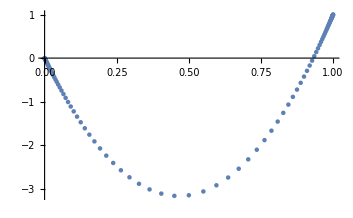

```mathematica
ListPlot[a]
```

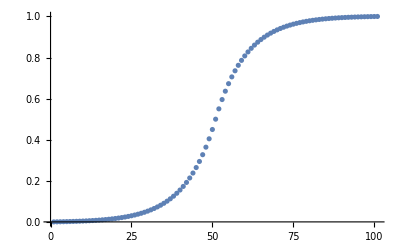

```mathematica
ListPlot[a[[;;,1]]]
```

```mathematica
A = Import["turb_out.txt","Table"];
```

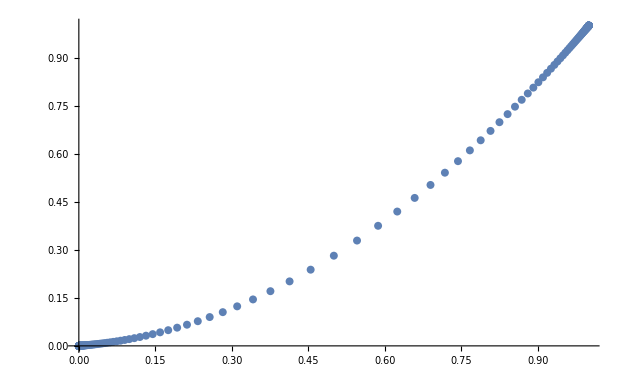

```mathematica
ListPlot[{A}]
```

```mathematica
a = Import["turb_out_plus.txt","Table"];
```

```mathematica
a[[;;,2]]=Abs[a[[;;,2]]];
```

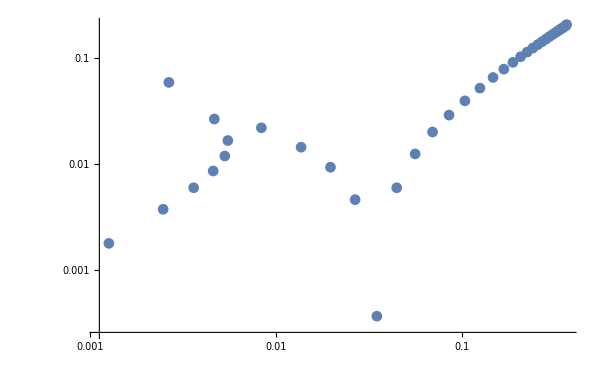

```mathematica
ListPlot[a, ScalingFunctions->{"Log","Log"}, PlotRange->All]
```

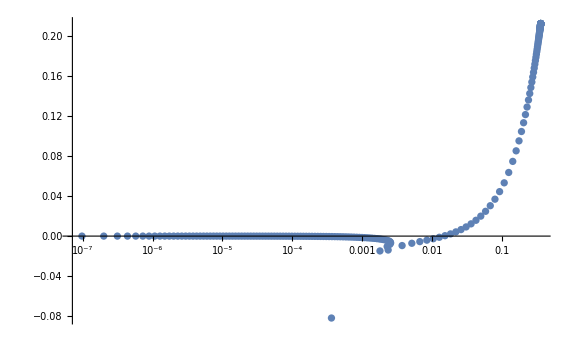

```mathematica
ListPlot[a, ScalingFunctions->{"Log",None}]
```